## Read in new results

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/npadmana/myWork/lowdiscrepancyRR/data/boss/lds_lowz_angular

```mathematica
a = Import["lowz_log_angular.dat","Table"]//Rest;
rrDat = Join[{{0.0,0.0}},a[[All,{2,3}]]];
rrAccum = Transpose[{rrDat[[All,1]],Accumulate[rrDat[[All,2]]]}];
```

```mathematica
rrDat[[1;;5]]//TableForm
rrAccum[[1;;5]]//TableForm
```

0. | 0.
0.00102329 | 8.32963×10^-11
0.00104713 | 8.72226×10^-11
0.00107152 | 9.13317×10^-11
0.00109648 | 9.56354×10^-11

0. | 0.
0.00102329 | 8.32963×10^-11
0.00104713 | 1.70519×10^-10
0.00107152 | 2.61851×10^-10
0.00109648 | 3.57486×10^-10

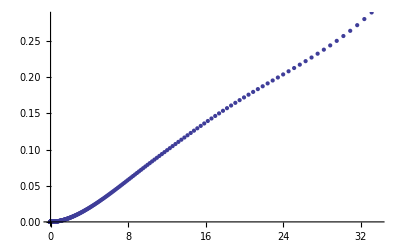

```mathematica
ListPlot[rrAccum]
```

```mathematica
Clear[rrInt];rrInt = Interpolation[rrAccum]
```

InterpolatingFunction[{{0.,100.}},<>]

```mathematica
Clear[rrFunc];rrFunc[r_] = D[rrInt[r],r]
```

InterpolatingFunction[{{0.,100.}},<>][r]

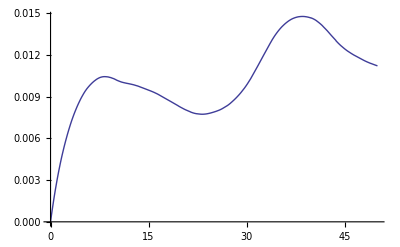

```mathematica
Plot[rrFunc[r],{r,0, 50}]
```

## Read in regular pair count data

```mathematica
b = Import["../angular/7-21_LOWZ-north-2011_06_10-randoms.dat"]//Rest//Select[#,#[[3]] > 10000 &] &;
```

```mathematica
b//Short//TableForm
```

{{0.004132,0.004863,11452.},{0.004863,0.005722,15936.},«45»,{8.69749,10.2353,1.59059×10^10}}

```mathematica
predict =#3/Integrate[rrFunc[r], {r,#1,#2} ]/10^12-1& @@@ b
```

{-0.0137036,-0.00727527,-0.0149805,0.000617407,0.00538843,-0.0110062,0.00519023,0.00871202,-0.00327276,0.00187273,0.00210082,0.00281707,0.00201541,0.000857928,0.00310824,0.000403012,0.000702704,-0.000397696,0.000224609,0.000974822,0.00144175,0.00148404,0.00141237,0.00130288,0.00132786,0.00121966,0.00127945,0.0011776,0.00129822,0.00135353,0.00159772,0.00173599,0.00186046,0.00166796,0.0017409,0.00147056,0.00128002,0.0013191,0.00179376,0.00209718,0.00244061,0.0024635,0.0023423,0.00262522,0.0033198,0.00353686,0.00321072,0.00314911}

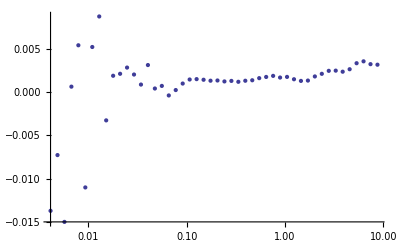

```mathematica
ListLogLinearPlot[Transpose[{b[[All,1]], predict}], PlotRange->All]
```